# vaje 4

# 1 naloga

```mathematica
trikotnik = Trikotnik[{0,0}, {5,1}, {7,4}]
```

Trikotnik[{0,0},{5,1},{7,4}]

```mathematica
Stranice[{AA_, BB_, CC_}] := {{AA, BB}, {BB, CC}, {CC, AA}}
```

```mathematica
a = {{0,0}, {5,1}}
b = {{5,1}, {7,4}}
c = {{7,4}, {0,0}}
```

```mathematica
Stranice[{{0,0}, {5,1}, {7,4}}]
```

{{{0,0},{5,1}},{{5,1},{7,4}},{{7,4},{0,0}}}

```mathematica
Koti[Trikotnik[AA_,BB_,CC_]] := {Kot[CC, AA, BB], Kot[AA, BB, CC], Kot[BB, CC, AA] }
```

```mathematica
alfa = Kot[{7,4}, {0,0}, {5,1}]
```

Kot[{7,4},{0,0},{5,1}]

```mathematica
Koti[Trikotnik[{0,0}, {5,1}, {7,4}]]
```

{Kot[{7,4},{0,0},{5,1}],Kot[{0,0},{5,1},{7,4}],Kot[{5,1},{7,4},{0,0}]}

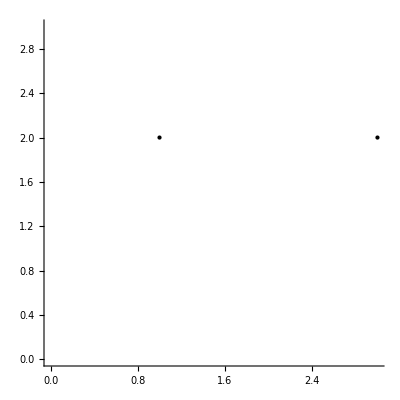

```mathematica
Graphics[{Point[{1,2}], Point[{3,2}]}, Axes -> True, PlotRange -> {{0,3},{0,3}}]
```

```mathematica
SlikaOglisc[Trikotnik[AA_,BB_,CC_]] := Graphics[{Point[AA], Point[BB], Point[CC]}]
```

```mathematica
SlikaOglisc[trikotnik]
```

-Graphics-

```mathematica
SlikaStranic[Trikotnik[AA_,BB_,CC_]] := Graphics[{Line[{AA, BB}], Line[{BB, CC}], Line[{CC, AA}]}]
```

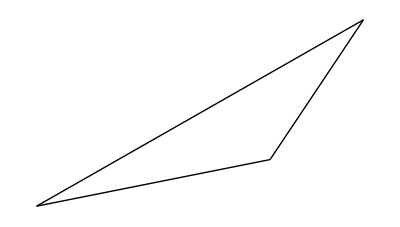

```mathematica
SlikaStranic[trikotnik]
```

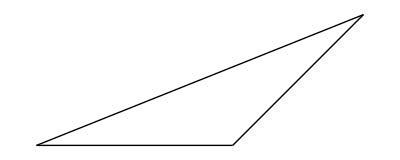

```mathematica
SlikaStranic[Trikotnik[{5,4},{3,2},{0,2}]]
```

```mathematica
ClearAll[NarisiTrikotnik]
```

```mathematica
NarisiTrikotnik[t_Trikotnik] := {SlikaOglisc[t], SlikaStranic[t]}
```

```mathematica
NarisiTrikotnik[trikotnik]
```

{-Graphics-,-Graphics-}

```mathematica
SlikaOglisc[Trikotnik[AA_,BB_,CC_]] := {Point[AA], Point[BB], Point[CC]}
SlikaStranic[Trikotnik[AA_,BB_,CC_]] := {Line[{AA, BB}], Line[{BB, CC}], Line[{CC, AA}]}
NarisiTrikotnik[t_Trikotnik] := Graphics[{SlikaOglisc[t], SlikaStranic[t]}]
```

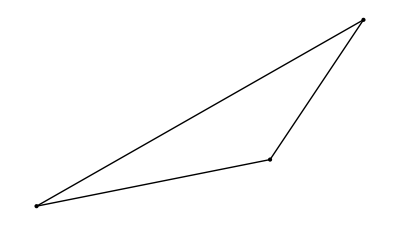

```mathematica
NarisiTrikotnik[trikotnik]
```

# 2 naloga

```mathematica
v = {1,2}
```

{1,2}

```mathematica
Sqrt[v.v]
```

√5

```mathematica
Norm[v]
```

√5

```mathematica
Dolzina[Daljica[AA_,BB_]] := Norm[BB - AA]
```

```mathematica
VelikostKota[Kot[AA_,BB_,CC_]] := ArcCos[(AA - BB).(CC - BB)/ (Norm[AA-BB]*Norm[CC-BB]) ]
```

```mathematica
VelikostKota[Kot[{1,1},{0,0},{1,0}]]
```

π/4

```mathematica
koti = Koti[trikotnik]
```

{Kot[{7,4},{0,0},{5,1}],Kot[{0,0},{5,1},{7,4}],Kot[{5,1},{7,4},{0,0}]}

```mathematica
beta = koti // First
```

Kot[{7,4},{0,0},{5,1}]

```mathematica
VelikostKota[beta]
```

ArcCos[3/(√10)]

```mathematica
vsikoti = Map [VelikostKota, koti]
```

{ArcCos[3/(√10)],(3 π)/4,ArcCos[2/(√5)]}

```mathematica
Apply[Plus, vsikoti] // N
```

3.14159

```mathematica
Pi // N
```

3.14159

```mathematica
Apply[Plus, vsikoti] // FullSimplify
```

π

```mathematica
VektorSimetraleKota[Kot[AA_,BB_,CC_],dol_] := Normalize[Normalize[AA - BB] + Normalize[CC - BB]] * dol
```

```mathematica
VektorSimetraleKota[Kot[{0,1},{0,0},{1,0}],Sqrt[2]]
```

{1,1}

```mathematica
PresecisceSimetraleKota[Kot[AA_,BB_,CC_]] := (t /.First[Solve[BB + k*VektorSimetraleKota[Kot[AA,BB,CC],1] == CC + t*(AA - CC),{k,t}]]) * (AA - CC)
```

```mathematica
PresecisceSimetraleKota[beta] // N
```

{0.774852,1.16228}

```mathematica
PresecisceSimetraleKota[Kot[AA_,BB_,CC_]] := Module[{enacba, resitev, t},
enacba = BB + k*VektorSimetraleKota[Kot[AA,BB,CC],1] == CC + t*(AA - CC);
resitev = Solve[enacba, {t,k}] //First;
t = t /. resitev;
CC + t * (AA - CC)
]
```

```mathematica
PresecisceSimetraleKota[beta]
```

{5-(2 (-(5 (1/(√26)+4/(√65)))/(√((1/(√26)+4/(√65))^2+(5/(√26)+7/(√65))^2))+(5/(√26)+7/(√65))/(√((1/(√26)+4/(√65))^2+(5/(√26)+7/(√65))^2))))/(-(2 (1/(√26)+4/(√65)))/(√((1/(√26)+4/(√65))^2+(5/(√26)+7/(√65))^2))+(3 (5/(√26)+7/(√65)))/(√((1/(√26)+4/(√65))^2+(5/(√26)+7/(√65))^2))),1-(3 (-(5 (1/(√26)+4/(√65)))/(√((1/(√26)+4/(√65))^2+(5/(√26)+7/(√65))^2))+(5/(√26)+7/(√65))/(√((1/(√26)+4/(√65))^2+(5/(√26)+7/(√65))^2))))/(-(2 (1/(√26)+4/(√65)))/(√((1/(√26)+4/(√65))^2+(5/(√26)+7/(√65))^2))+(3 (5/(√26)+7/(√65)))/(√((1/(√26)+4/(√65))^2+(5/(√26)+7/(√65))^2)))}

```mathematica
slika1 = NarisiTrikotnik[trikotnik]
```

-Graphics-

```mathematica
slika2 = Graphics[Point[PresecisceSimetraleKota[beta]]]
```

-Graphics-

```mathematica
tocka = PresecisceSimetraleKota[beta]
```

{5-(2 (-(5 (1/(√26)+4/(√65)))/(√((1/(√26)+4/(√65))^2+(5/(√26)+7/(√65))^2))+(5/(√26)+7/(√65))/(√((1/(√26)+4/(√65))^2+(5/(√26)+7/(√65))^2))))/(-(2 (1/(√26)+4/(√65)))/(√((1/(√26)+4/(√65))^2+(5/(√26)+7/(√65))^2))+(3 (5/(√26)+7/(√65)))/(√((1/(√26)+4/(√65))^2+(5/(√26)+7/(√65))^2))),1-(3 (-(5 (1/(√26)+4/(√65)))/(√((1/(√26)+4/(√65))^2+(5/(√26)+7/(√65))^2))+(5/(√26)+7/(√65))/(√((1/(√26)+4/(√65))^2+(5/(√26)+7/(√65))^2))))/(-(2 (1/(√26)+4/(√65)))/(√((1/(√26)+4/(√65))^2+(5/(√26)+7/(√65))^2))+(3 (5/(√26)+7/(√65)))/(√((1/(√26)+4/(√65))^2+(5/(√26)+7/(√65))^2)))}

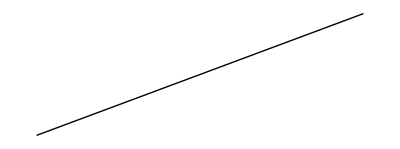

```mathematica
slika3 = Graphics[Line[{{0,0}, tocka}]]
```

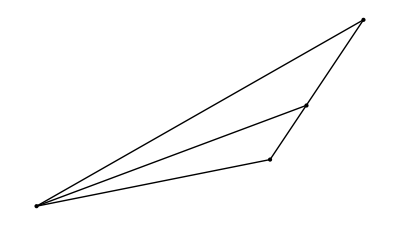

```mathematica
Show[slika1,slika2,slika3]
```

```mathematica
SlikaDaljiceSimetraleKota[Kot[AA_,BB_,CC_]] := Line[{BB,PresecisceSimetraleKota[Kot[AA,BB,CC]]}]
```

```mathematica
SlikaDaljiceSimetraleKota[beta] // FullSimplify
```

Line[{{0,0},{11/3+(2 √10)/3,-1+√10}}]

```mathematica
SlikaSimetralKotov[trikotnik_Trikotnik] := Module[{koti},
koti = Koti[trikotnik];
daljice = Map[SlikaDaljiceSimetraleKota, koti]
]
```

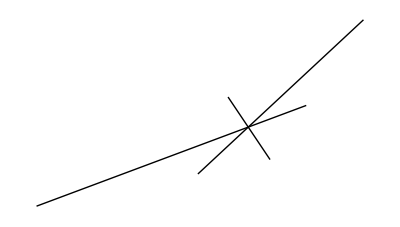

```mathematica
slika4 = Graphics[SlikaSimetralKotov[trikotnik]]
```

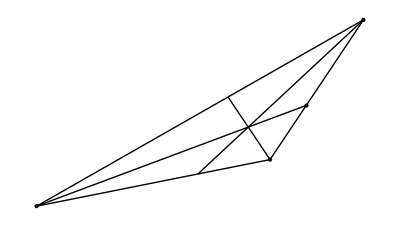

```mathematica
Show[slika1,slika2,slika4]
```

```mathematica
NarisiTrikotnikSSimetralami[trikotnik_Trikotnik] := Graphics[
{SlikaOglisc[trikotnik],
SlikaStranic[trikotnik],
SlikaSimetralKotov[trikotnik]},
 AspectRatio-> Automatic, PlotRange->{{-7,7},{0,7}}]
```

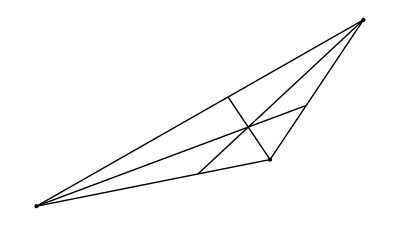

```mathematica
NarisiTrikotnikSSimetralami[trikotnik]
```

```mathematica
Manipulate[NarisiTrikotnikSSimetralami[Trikotnik[{0,0}, {5,1}, {cx,cy}]],{cx, -7,7},{cy,3,6}]
```